## doi: 10.1063/1.456483

```mathematica
Clear["Global`*"]
```

```mathematica
(*Clear["Global`*"]*)
massunit=1/5.48579911000000039*10^4;
KtoEh=3.1668153 10^(-6);
cmtoEh=4.556335252 10^(-6);
BtoA=0.529177;
eVtocm=8.06554465*10^3;
autofs = 0.02418884326505;
autos=2.4188843265;
05/10^17;
autoMHz =  6.579683918175572*10^9;
autoVpm=5.14220624463189208 10^11;
autoD=2.54174622886413859035;
alphaFine=1/137.035999084;
a0 = 5.291772109 10^(−11);
Eh= 4.35974380 10^(−18);
ℏ = 1.0545718 10^(-34);
u = 1.6605402 10^(-27);
prefixDirectory = "C:\\Users\\jacek\\Dropbox\\Jacek_Gebala\\TBP";
```

### 1. Initalize

```mathematica
Clear[ρ,α,θξ,ϕξ,θη,ϕη];
(*initalize Directory*)
SetDirectory["C:\\Users\\jacek\\Dropbox\\Jacek_Gebala\\TBP"];



(*initialize input potentials and systems parameters*)
Vpol[r_,α_,ρ_]:= -α/(2r^4) (1 - Exp[-(r/ρ)^6] );
VLJ[r_,Re_,De_]:= 4De ((Re/r)^12/4- (Re/r)^6/2);
VTB[ar_,D_,r0_]:= -D(Sech[ar/r0])^2 ;

aK2Tiemann = Import["V_a_K2_Tiemann.dat"];
XK2Tiemann = Import["V_X_K2_Tiemann.dat"];
VaK2Tiemann=Interpolation[aK2Tiemann];
VXK2Tiemann=Interpolation[XK2Tiemann];


TestFun[name_,Coord_]:=name[Sequence@@Coord]; (* <- one can define any function name[Coord] and check that the code works *)



(*Initalize general definitions of vectors*)
r[i_] := {x[i],y[i],z[i]};
vec[name_]:={name[1],name[2],name[3]};
vec2d[name_]:={name[1],name[2]};

(*Initialize masses of 3 particles*)
massList={38.963707,39.963998};
massList={39.963998};
m1 = massList[[1]]*massunit; m2 = m3 = m1;
mred3=(m1 m2 m3/(m1+m2+m3))^(1/2);
mred=m1*m2/(m1+m2);
d3 = (m3/mred3 * (m1+m2)/(m1+m2+m3))^(1/2);
ϕ12 = 2 ArcTan[m2/mred3];
ϕ31 = -2 ArcTan[m3/mred3];

(*Inverse the Jacobi transformation and define the hyperspherical map*)
invJacobiCoordMap = Simplify[Solve[ξ==Simplify[(m1 m2 / (m1 + m2))^0.5 (vr[1]-vr[2])] && η==Simplify[(m3(m1 + m2)/(m1 + m2 + m3))^0.5 (  (m1 vr[1] + m2 vr[2])/(m1+m2) - vr[3] )] &&
									Rcm==Simplify[(m1 vr[1] + m2 vr[2] + m3 vr[3] )/(m1+m2+m3)], {vr[1],vr[2],vr[3]} ]⟦1⟧
							 ];
							 		 		 
							 		 		 		 		 
HypSpherMap = {
				ξ[1] ->  ρ Cos[α] Sin[θξ] Cos[ϕξ],
				ξ[2] ->  ρ Cos[α] Sin[θξ] Sin[ϕξ],
				ξ[3] ->  ρ Cos[α] Cos[θξ] ,
				η[1] ->  ρ Sin[α] Sin[θη] Cos[ϕη],
				η[2] ->  ρ Sin[α] Sin[θη] Sin[ϕη],
				η[3] ->  ρ Sin[α] Cos[θη]
				};
HypPlanePrlMap = {
				ξ[1] ->  ρ/mred3^(1/2) Cos[π/4-θ/2] Cos[ϕ/2 + ϕ12/2],
				ξ[2] ->  ρ/mred3^(1/2) Sin[π/4-θ/2] Sin[ϕ/2 + ϕ12/2],
				ξ[3] ->  0. ,
				η[1] ->  ρ/mred3^(1/2) Cos[π/4-θ/2] Sin[-ϕ/2 - ϕ12/2],
				η[2] ->  ρ/mred3^(1/2) Sin[π/4-θ/2] Cos[ϕ/2 + ϕ12/2],
				η[3] ->  0.
};	

(*Find \vec{r}_i in Jacobi coords*)
invJacr[i_] := Chop[invJacobiCoordMap⟦i,2⟧]/.{η->vec[η],ξ->vec[ξ]} ;
invJacr[i_,j_]:= (Chop[invJacobiCoordMap⟦i,2⟧-invJacobiCoordMap⟦j,2⟧])/.{η->vec[η],ξ->vec[ξ]};


(* Find |\vec{r}_i - \vec{r}_j| in hyperspherical coords using inverse Jacobi transformation and the hyperspherical map *)

lthSq[vec_]:= Sum[vec⟦i⟧^2,{i,Length[vec]}] ; (*<-- Norm of a vector*)
r[i_,j_]:=FullSimplify[(lthSq[invJacr[i,j]]/.HypSpherMap)^(1/2),Assumptions->{Im[ρ]==0,ρ>0,0≤α≤π/2,0≤θξ≤π,0≤ϕξ≤2π,0≤θη≤π,0≤ϕη≤2π}];


(* Define hyperspherical harmonics globally*)
Nlλk=(2 κ! 4^(k+2) (k+2) (l+λ+κ+1)! (l+κ+1)! (λ+κ+1)! /(π (2l+2κ+2)! (2λ+2κ+2)!))^(1/2);
Φ[α_,θξ_,ϕξ_,θη_,ϕη_]:= SphericalHarmonicY[l,m,θξ,ϕξ] SphericalHarmonicY[λ,μ,θη,ϕη] Nlλk  (Cos[α])^l (Sin[α])^λ JacobiP[κ,l+1/2,λ+1/2,-Cos[2α]];

coeffN[l_,λ_,k_]:=(2 ((k - l - λ)/2)! 4^(k+2) (k+2) (l+λ+((k - l - λ)/2)+1)! (l+((k - l - λ)/2)+1)! (λ+((k - l - λ)/2)+1)! /(π (2l+2((k - l - λ)/2)+2)! (2λ+2((k - l - λ)/2)+2)!))^(1/2);
HypAngPhi[α_,θξ_,ϕξ_,θη_,ϕη_,l_,m_,λ_,μ_,k_]:= FullSimplify[SphericalHarmonicY[l,m,θξ,ϕξ] SphericalHarmonicY[λ,μ,θη,ϕη] coeffN[l,λ,k]  (Cos[α])^l (Sin[α])^λ JacobiP[((k - l - λ)/2),l+1/2,λ+1/2,-Cos[2α]]];
```

### 2.Try to diagnolize w.r.t. to νν’

#### a/ Solve hyperangular problem in body-fixed frame

```mathematica
(*------------Initialize matrices and fun's------*)
NJxSqN[J_,nN_]:= (1/2)(J(J+1)-nN^2);
NJxSqNp2[J_,nN_]:= (1/4)((J-nN)(J-nN-1)(J+nN+1)(J+nN+2))^(1/2) ;

HTh[x_,y_]:= Piecewise[{{1,x-y≥0},{0,x-y<0}}];
δ[x_,y_]:= KroneckerDelta[x,y] ; 
CFunAs[k_,x_,K_]:=((K+x)/2+2+k)((K-x)/2-k);
CFun[nN_,k_,ν_,K_]:= HTh[nN,ν] CFunAs[k,nN,K] + (1-HTh[nN,ν]) CFunAs[k,ν,K] ;

V[J_,s_,nN_]:= WignerD[{J,s,nN},0,π/2,0];
	tensV[J_] := Table[V[J,s,nN],{nN,-J,J},{s,-J,J}];
	vecV[J_,s_]:=Table[V[J,s,nN],{nN,-J,J}];
	
ns[J_,K_,ν_]:= Floor[ If[EvenQ[K]&& OddQ[J+(K-ν)/2],(J-jp)/2,(J+2-jp)/2]];
	
kN[K_,ν_,nN_]:=Piecewise[{{(K-ν)/2,nN<ν},{(K-nN)/2,nN≥ν}}];
kmax[K_,ν_]:=(K-ν)/2;
(*-------------------Initialize------------------*)
totFmatrix={};

For[J=0,J≤20,J++,
	
	FJmatrix={};
	For[K  = J,K≤38,K++,
		FKmatrix={};sKmatrix={};
		Print["J = ",J," / K = ",K];
		For[ν=If[EvenQ[K],0,1],ν≤K,ν=ν+2,
			Fνmatrix={};
(*------------Define path K+J odd/even----------*)
If[EvenQ[K+J],nNvec = Table[x,{x,-J,J,2}], nNvec = Table[x,{x,-J+1,J-1,2}] ];
If[EvenQ[K+J],jp=0,jp=1];
If[ν≥J,deltaν=1,deltaν=0];

If[EvenQ[K+J],
  Which[
	EvenQ[(K-Abs[ν])/2]&&(K-Abs[ν])/2 ≥ J, nI[J_,K_,ν_]:= Floor[ (J+2)/2];        ,
	 OddQ[(K-Abs[ν])/2]&&(K-Abs[ν])/2 ≥ J, nI[J_,K_,ν_]:= Floor[ (J+1)/2];        ,
	(K-Abs[ν])/2 < J   &&(K+Abs[ν])/2 ≥ J, nI[J_,K_,ν_]:= Floor[ (K-Abs[ν]+4)/4];,
	(K+Abs[ν])/2 < J                     , nI[J_,K_,ν_]:=(K-J+2)/2;
	];
	smax = nI[J,K,ν]-1;
	Vpm[J_,s_,nN_] := If[s>0,Sqrt[2],1] V[ J,s,J-2nN];
,	
  Which[
	EvenQ[(K-Abs[ν])/2]&&(K-Abs[ν])/2 ≥ J, nI[J_,K_,ν_]:= Floor[ J/2];            ,
	 OddQ[(K-Abs[ν])/2]&&(K-Abs[ν])/2 ≥ J, nI[J_,K_,ν_]:= Floor[(J+1)/2];         ,
	(K-Abs[ν])/2 < J   &&(K+Abs[ν])/2 ≥ J, nI[J_,K_,ν_]:= Floor[ (K-Abs[ν]+2)/4];,
	(K+Abs[ν])/2 < J                     , nI[J_,K_,ν_]:= (K-J+1)/2;
	];
	smax = nI[J,K,ν];
	Vpm[J_,s_,nN_]:= Sqrt[2]V[J,s,J-2nN+1]; 
];
sVec = Table[x,{x,jp,smax}];
(*-------------------Steps----------------------*)
(*1 and 2*)
	(*Print["V^ω = ",Vω=Table[Vpm[J,sVec⟦sInd⟧,x],{x,jp,J}]];*)
(*3*)
	(*Print["number of solutions ns = ",ns[J,K,ν]];*)
	(*Print["kMax = ",kmax[K,ν]];*)
(*4*)	
	(*Print["number of independent solutions nI = ",nI[J,K,ν]];*)
	(*Print["smax = ",smax];	*)
(*5*)
(*Print["          N's: ",nNvec];*)

A[k_]:=SparseArray[{{i_,i_}->k^2 - NJxSqN[J,  nNvec⟦1⟧+2(i-1) ], {i_,j_}/;j==i+1-> - NJxSqNp2[J,nNvec⟦1⟧+2(i-1)], {i_,j_}/;j==i-1-> - NJxSqNp2[J,nNvec⟦1⟧+2(i-1)-2]   }  ,{Length[nNvec],Length[nNvec]}]//N;
B[k_]:=SparseArray[{{i_,i_}-> ((1-HTh[ nNvec⟦1⟧+2(i-1),ν])*( nNvec⟦1⟧+2(i-1)) + HTh[ nNvec⟦1⟧+2(i-1),ν]*ν)(k+1/2) , {i_,j_}/;j==i+1-> -NJxSqNp2[J, nNvec⟦1⟧+2(i-1)]*(1-HTh[ nNvec⟦1⟧+2(i-1),ν]), {i_,j_}/;j==i-1-> NJxSqNp2[J, nNvec⟦1⟧+2(i-1)-2]*HTh[ν, nNvec⟦1⟧+2(i-1)]   }  ,{Length[nNvec],Length[nNvec]}]//N;
cC[k_]:=SparseArray[{{i_,i_}->  CFun[ nNvec⟦1⟧+2(i-1),k,ν,K], {i_,j_}/;j==i+1-> NJxSqNp2[J, nNvec⟦1⟧+2(i-1)]*HTh[ nNvec⟦1⟧+2(i-1),ν]}  ,{Length[nNvec],Length[nNvec]}]//N;


(*Print["   Highest powers in polynomial: " ,highestPowersTable=Table[ kN[K,ν,nNvec⟦1⟧+2x] ,{x,0,-1+Length[nNvec]}]];*)


mainRecurrenceFun[initCoeffs_,J_,K_,ν_,jp_]:=Module[{bInMatrixModule,bInitial,bMatrix,bVecIt,bVecItP1,bVecLocal,bVecTemp,bNikm2,bNip2km2,q,ki,Ni,startNi},

			bInMatrixModule={};
			
			For[q=1,q≤ns[J,K,ν],q++,
				(*Print["A function f(q) of the solution number, where δ[N,f(q)]; f(q) = ",J+2-jp-2 q];*)

				Clear@i;
				
				bInitial=initCoeffs[J,K,ν,jp,q];
				bMatrix={Table[Piecewise[{{bInitial⟦x+1⟧,nNvec⟦x+1⟧≤ν}}],{x,0,Length[nNvec]-1}]};
				bVecIt=bMatrix⟦1⟧;
				bVecItP1 = Table[0,Length[nNvec]];
				(*Print["Inital+1 bVec = ",bVecItP1];*)
				(*Print["Inital bVec = ",bVecIt//N];*)

				For[ki=kmax[K,ν]+1,ki-2≥kN[K,ν,nNvec⟦Length[nNvec]⟧],ki=ki-1,
						startNi=    Position[nNvec,ν]⟦1,1⟧+ Abs[ki-2-kmax[K,ν]];
						bVecTemp=Join[{bInitial⟦startNi⟧},Table[0,Abs[Length[nNvec]-startNi]]];
						bNip2km2=  bInitial⟦startNi⟧;
						For[Ni= startNi-1 ,Ni≥1 ,Ni=Ni-1,
								bNikm2= var/.Solve[ (A[ki].bVecItP1)⟦Ni⟧+(B[ki-1].bVecIt)⟦Ni⟧+cC[ki-2]⟦Ni,Ni+1⟧*bNip2km2 + cC[ki-2]⟦Ni,Ni⟧  var == 0  ,var]⟦1,1⟧;
								PrependTo[bVecTemp,bNikm2];
								bNip2km2 =  bNikm2;
							];
						PrependTo[bMatrix,bVecTemp];

						bVecItP1=bVecIt;
						bVecIt=bVecTemp;
					];

				For[ki,ki-1≥0,ki=ki-1,
					bVecLocal  = (-Inverse[cC[ki-2]].(A[ki].bVecItP1 + B[ki-1].bVecIt) );

					If[ki-2≥0,PrependTo[bMatrix,bVecLocal]];
					bVecItP1 = bVecIt;
					bVecIt = bVecLocal;
					];

(*Print[bMatrix//N//MatrixForm];*)
				AppendTo[bInMatrixModule,bMatrix];
				];
			Return[bInMatrixModule]];

initDeltaVec[J_,K_,ν_,jp_,q_] := Table[    Piecewise[{{   δ[-nNvec⟦1⟧-2x,(J+2-jp-2 q)],nNvec⟦1⟧+2x≤0},{(-1)^(-kN[K,ν,nNvec⟦1⟧+2x]-J) δ[nNvec⟦1⟧+2x,(J+2-jp-2 q)],nNvec⟦1⟧+2x>0}}]  ,{x,0,Length[nNvec]-1}];
bInMatrix = mainRecurrenceFun[initDeltaVec,J,K,ν,jp];

(*6*)
wMatrix = {};
bInMax = Max[Abs[bInMatrix//N]];

RslvMatrixInit[as_] := Join[
				Table[bInMatrix⟦aq,as+1,aN⟧   ,{aN,1,Length[nNvec]},{aq,1,Length[bInMatrix]}],
				If[smax≠jp &&  as>jp,
					Table[ bInMatrix⟦aq,as,aN⟧    ,{aN,1,Length[nNvec]},{aq,1,Length[bInMatrix]}]
					,{}]
			];
RslvMatrix=RslvMatrixInit[smax];
(*Print[RslvMatrix//N//MatrixForm];*)

For[si=smax,si≥jp,si=si-1,
		
		
		Vωs=Table[Vpm[J,si,x],{x,jp,J}];
		RslvVecIn = Join[Vωs,If[smax≠jp, Table[0,If[si≠jp,Length[nNvec],0] + (smax-si) ],{}] ];
		(*Print[RslvVecIn//N];*)


		RslvVec=(PseudoInverse[RslvMatrix].RslvVecIn);
		AppendTo[wMatrix,RslvVec];
		(*Print[RslvVec //N];*)
		
		If[si>jp,
			RslvMatrix = Join[RslvMatrixInit[si-1],bInMax/(3*Max[Abs[wMatrix//N]]) wMatrix ]
			(*;
			Print[RslvMatrix//N//MatrixForm];*)
		];
];
(*Print[wMatrix // N //MatrixForm];*)


	For[NInd=1,NInd≤Length[nNvec],NInd++,
		(*polMatrix={};*)
		(*polPrimMatrix={};*)
		FNmatrix={};

		For[sInd=Length[wMatrix],sInd≥1,sInd=sInd-1,

			(*Print["polynomials W  for:    ","N = ",nNvec⟦NInd⟧,"   ν = ",ν," s  = ",sVec⟦sInd⟧,"    "];*)
			(*AppendTo[polMatrix,Sum[   wMatrix⟦sInd,aQ⟧  Chop[Sum[bInMatrix⟦aQ,xk+1,NInd⟧ vU^(xk),{xk,0,Length[bInMatrix⟦aQ⟧]-1}]//N],{aQ,1,ns[J,K,ν]}]//FullSimplify//Chop];*)
			AppendTo[FNmatrix,   (1+vU)^((ν+nNvec⟦NInd⟧)/4)*(1-vU)^(Abs[ν-nNvec⟦NInd⟧]/4)*Sum[   wMatrix⟦sInd,aQ⟧  Chop[Sum[bInMatrix⟦aQ,xk+1,NInd⟧ vU^(xk),{xk,0,Length[bInMatrix⟦aQ⟧]-1}]//N],{aQ,1,ns[J,K,ν]}]//FullSimplify//Chop];
			(*initwMatrixVec[J_,K_,ν_,jp_,q_] := Table[Piecewise[{{wMatrix⟦sInd,(J+nNvec⟦x⟧+2-jp)/2⟧//N,nNvec⟦x⟧<0},{(-1)^(-kN[K,ν,nNvec⟦x⟧]-J) wMatrix⟦sInd,(J-nNvec⟦x⟧+2-jp)/2⟧//N,nNvec⟦x⟧>0},{wMatrix⟦sInd,(J+2-jp)/2⟧//N ,Not[EvenQ[K]&& OddQ[J+(K-ν)/2]] && nNvec⟦x⟧==0}}],{x,1,Length[nNvec]}];
			bInRegMatrix = mainRecurrenceFun[initwMatrixVec,J,K,ν,jp];
			AppendTo[polPrimMatrix,1/ns[J,K,ν] Sum[  Chop[Sum[bInRegMatrix⟦aQ,xk+1,NInd⟧ vU^(xk),{xk,0,Length[bInRegMatrix⟦aQ⟧]-1}]//N],{aQ,1,ns[J,K,ν]}]//FullSimplify//Chop];*)
			];
			AppendTo[Fνmatrix,FNmatrix];
			];
		AppendTo[sKmatrix,sVec];
		AppendTo[FKmatrix,Fνmatrix];
		];
		νInit = If[EvenQ[K],1,0];
		FKmatrix = Join[Table[  (-1)^(J+sKmatrix⟦nuInd,sSInd⟧)*FKmatrix⟦nuInd,nNInd,sSInd⟧  ,{nuInd,νInit+1,Length[FKmatrix]},{nNInd,Length[FKmatrix⟦nuInd⟧],1,-1},{sSInd,1,Length[FKmatrix⟦nuInd,nNInd⟧]}],FKmatrix];
		
		AppendTo[FJmatrix,FKmatrix];
	];
	AppendTo[totFmatrix,FJmatrix];
];
```

#### b/ Invoke > Load_Fmatrices_from_cloud.nb

#### c/ Construct H_ad hamiltonian and diagonalize

```mathematica
QuantumList=Join[Flatten[OrNormFmatrix[1],3],Flatten[OrNormFmatrix[2],3],Flatten[OrNormFmatrix[3],3],Flatten[OrNormFmatrix[4],3]];(*HARDCODE Jmax=4!!!!!!!!!!!!!!*)
modelSet={1,2,3,5};
compareSetOfQuantum[{a1_,a2_,a3_,a4_},{b1_,b2_,b3_,b4_}]:= Which[a1>b1,Return[1],a1<b1,Return[-1],
																  a2>b2,Return[1],a2<b2,Return[-1],
																  a3>b3,Return[1],a3<b3,Return[-1],
																  a4>b4,Return[1],a4<b4,Return[-1],
																  True,Return[0]];
																  
binarySearchQuantumList[QList_,{aJ_,aK_,aν_,as_}]:=Module[{finalList,lower,upper,current,isBigger},
															lower=1;upper=Length[QList];
															While[True, 
																current=Floor[lower/2+upper/2];
																isBigger=compareSetOfQuantum[Table[QList⟦current,modelSet⟦i⟧ ⟧,{i,1,Length[modelSet]}],{aJ,aK,aν,as}];
																Which[											
																		isBigger==1,upper=current,
																	   isBigger== -1,lower=current,
																	   isBigger==0,Break[]
																];
																
																];
															lower=upper=current;
															While[lower>1 && compareSetOfQuantum[Table[QList⟦lower-1,modelSet⟦i⟧ ⟧,{i,1,Length[modelSet]}],{aJ,aK,aν,as}]==0,lower=lower-1
																];
														    While[upper<Length[QList]-1&&compareSetOfQuantum[Table[QList⟦upper+1,modelSet⟦i⟧ ⟧,{i,1,Length[modelSet]}],{aJ,aK,aν,as}]==0,upper=upper+1
																];
															Return[Table[Last[QList⟦i⟧],{i,lower,upper}]];
															];
FListMap=Association[{}]
ii=0;
For[JInd=1,JInd≤9,JInd++,(*HARDCODE Jmax=9!!!!!!!!!!!!!!*)
	For[KInd=1,KInd≤Length[OrNormFmatrix[JInd]],KInd++,
		For[νInd=1,νInd≤Length[OrNormFmatrix[JInd]⟦KInd⟧],νInd++,
			For[sInd=1,sInd≤Length[OrNormFmatrix[JInd]⟦KInd,νInd⟧],sInd++,
				ii+=1;
				AssociateTo[FListMap,{{ OrNormFmatrix[JInd]⟦KInd,νInd,sInd,1,1⟧, OrNormFmatrix[JInd]⟦KInd,νInd,sInd,1,2⟧, OrNormFmatrix[JInd]⟦KInd,νInd,sInd,1,3⟧, OrNormFmatrix[JInd]⟦KInd,νInd,sInd,1,5⟧}->  Table[Last[OrNormFmatrix[JInd]⟦KInd,νInd,sInd,i⟧ ],{i,1,Length[OrNormFmatrix[JInd]⟦KInd,νInd,sInd⟧]}]} ]
				];
			];
		];
	];
```

<||>

```mathematica
Clear@r12; Clear@r23; Clear@r31;
mred3
```

42059.9

```mathematica
QuantumList[[16]]
Length[Flatten[OrNormFmatrix[1],3]]
QuantumList[[Length[Flatten[OrNormFmatrix[1],3]]]]
```

{0,10,-10,0,0,0.0120943 (1-vU^2)^(5/2)}

210

{0,38,38,0,0,0.0403144 (1-vU^2)^(19/2)}

```mathematica
(*Potential parameters*)
De = .03;
ρ0=2;
gridFun[r_]:=Log[r];r00=0.15;rr=65.;nMax=50;

VTBfileName = "VTB_D_"<>ToString[De]<>"_r0_"<>ToString[ρ0]<>".dat"

VXK2TiemannfileName = "VXK2Tiemann_data.dat"

fileVTB=OpenWrite[prefixDirectory<>"\\outputs\\"<>VTBfileName];
fileVXK2=OpenWrite[prefixDirectory<>"\\outputs\\"<>VXK2TiemannfileName];

dataVTB=Table[  {Exp[gridFun[r00]+ni*(gridFun[rr]-gridFun[r00])/nMax],VTB[Exp[gridFun[r00]+ni*(gridFun[rr]-gridFun[r00])/nMax],De,ρ0 ]  },{ni,1,nMax}];
dataVXK2=Table[  {Exp[gridFun[r00]+ni*(gridFun[rr]-gridFun[r00])/nMax],VXK2Tiemann[Exp[gridFun[r00]+ni*(gridFun[rr]-gridFun[r00])/nMax]] }  ,{ni,1,nMax}];

Export[fileVTB,dataVTB];Export[fileVXK2,dataVXK2];
Close[fileVXK2];Close[fileVTB];
(*
Plot[VTB[x,De,ρ0],{x,0,25}]
Plot[VXK2Tiemann[x],{x,5,25}]*)

C4 = 315.631468 / 2;
R4=Sqrt[2 C4 mred]
```

VTB_D_0.03_r0_2.dat

VXK2Tiemann_data.dat

3390.7

```mathematica
QuantumList[[1161]]
Length[Flatten[OrNormFmatrix[1],3]]+Length[Flatten[OrNormFmatrix[2],3]]
```

{2,2,-2,-2,0,0.00493749 (1+vU)}

1160

```mathematica
(*Assumption: m1=m2=m3=Subscript[m, He]*)
r12[aρ_,au_,aϕ_]:=( (aρ^2 (1+Sqrt[1-au^2]*Sin[aϕ]))/(√3))^(1/2);
r12[aρ_,au_,aϕ_]:= 3^(-1/4)*aρ*(1+Sqrt[1-au^2]*Sin[aϕ-π/6])^(1/2);
r23[aρ_,au_,aϕ_]:=((aρ^2 (2-Sqrt[1-au^2]*(√3 Cos[aϕ]+Sin[aϕ])))/(2 √3))^(1/2);
r23[aρ_,au_,aϕ_]:=3^(-1/4)*aρ*(1+Sqrt[1-au^2]*Sin[aϕ-5*π/6])^(1/2);
r31[aρ_,au_,aϕ_]:=((aρ^2 (2+Sqrt[1-au^2]*(√3 Cos[aϕ]-Sin[aϕ])))/(2 √3))^(1/2);
r31[aρ_,au_,aϕ_]:=3^(-1/4)*aρ*(1+Sqrt[1-au^2]*Sin[aϕ+π/2])^(1/2);

Vtot[aρ_,au_,aϕ_]:= VTB[ r12[aρ,au,aϕ],De,ρ0 ]+VTB[ r23[aρ,au,aϕ],De,ρ0 ]+VTB[r31[aρ,au,aϕ],De,ρ0]  ;
(*Vtot[aρ_,au_,aϕ_]:= VXK2Tiemann[ r12[aρ,au,aϕ]]+VXK2Tiemann[ r23[aρ,au,aϕ]]+VXK2Tiemann[ r31[aρ,au,aϕ]];*)

(*r00=0.15;
rr=65.;
nMax=50;*)
gridFun[r_]:=Log[r];
LengthOfBasisSet=35;
offset = 0 +Length[Flatten[OrNormFmatrix[1],3]]+Length[Flatten[OrNormFmatrix[2],3]];

DiagPartAdiabatic[aρ_]:= SparseArray[ {{i_,i_}:> N[(QuantumList⟦offset+i,2⟧ *(QuantumList⟦offset+i,2⟧ +4)+15/4  )/(2*mred3*aρ^2) ]} ,{LengthOfBasisSet,LengthOfBasisSet}];
HAdiabaticMatrix[aρ_]:=Array[(  If[ QuantumList⟦offset+#1,1⟧==QuantumList⟦offset+#2,1⟧&& Mod[QuantumList⟦offset+#1,2⟧,2]==Mod[QuantumList⟦offset+#2,2⟧,2] ,
								Flist=  FListMap[   Table[  QuantumList⟦offset+#1,modelSet⟦k⟧ ⟧,{k,1,Length[modelSet]}]  ];
								FlistPrim= FListMap[   Table[  QuantumList⟦offset+#2,modelSet⟦k⟧ ⟧,{k,1,Length[modelSet]}]];
								If[Length[Flist]≠ Length[FlistPrim],Print["Length[Flist]≠ Length[FlistPrim]"]; ];(*Tu się może zepsuć ^*)
								
								sumFun=vU*Sum[ Flist⟦i⟧*FlistPrim⟦i⟧ ,{i,1,Length[Flist]}];
								8 π^2/(2*QuantumList⟦offset+#1,1⟧+1)*NIntegrate[Exp[I*(QuantumList⟦offset+#1,2⟧-QuantumList⟦offset+#1,2⟧)*ϕ/2]*sumFun * Vtot[aρ,vU,ϕ],{vU,0,1},{ϕ,0,2*π/3},AccuracyGoal->8,Method->{"Trapezoidal"}]
									,0]   )&           ,{LengthOfBasisSet,LengthOfBasisSet}];

UνEigenList[LengthOfBasisSet]={};
For[ni=1,ni≤nMax,ni++,

	AppendTo[UνEigenList[LengthOfBasisSet],Eigensystem[       DiagPartAdiabatic[Exp[gridFun[r00]+ni*(gridFun[rr]-gridFun[r00])/nMax]]+HAdiabaticMatrix[Exp[gridFun[r00]+ni*(gridFun[rr]-gridFun[r00])/nMax]]  ]  ];
Print["ni: ",ni," / ρ = ",  Exp[gridFun[r00]+ni*(gridFun[rr]-gridFun[r00])/nMax] ," /  number of channels = ",Length[UνEigenList[LengthOfBasisSet]⟦ni,1⟧] ];
]
(*
Eigensystem[(DiagPartAdiabatic[R]+HAdiabaticMatrix[R])]*)
```

{{0.169367,0.0148157},{0.191234,0.0116212},{0.215924,0.00911542},{0.243802,0.00714996},{0.275279,0.00560829},{0.310821,0.00439904},{0.350951,0.00345052},{0.396262,0.00270653},{0.447424,0.00212289},{0.505191,0.00166514},{0.570417,0.00130609},{0.644063,0.00102446},{0.727219,0.000803556},{0.82111,0.000630283},{0.927124,0.000494371},{1.04683,0.000387765},{1.18198,0.000304146},{1.33459,0.000238557},{1.5069,0.000187112},{1.70145,0.000146757},{1.92113,0.000115105},{2.16917,0.0000902787},{2.44923,0.0000707172},{2.76545,0.00005546},{3.1225,0.0000434949},{3.52565,0.0000341114},{3.98084,0.0000267513},{4.49481,0.0000210356},{5.07514,0.0000164692},{5.73039,0.0000129238},{6.47025,0.0000100717},{7.30563,7.90996×10^-6},{8.24886,6.13784×10^-6},{9.31387,4.85184×10^-6},{10.5164,3.84277×10^-6},{11.8742,3.01262×10^-6},{13.4072,2.36428×10^-6},{15.1383,1.85449×10^-6},{17.0928,1.45463×10^-6},{19.2996,1.14098×10^-6},{21.7914,8.94967×10^-7},{24.6049,7.01995×10^-7},{27.7817,5.50632×10^-7},{31.3686,4.31905×10^-7},{35.4186,3.38778×10^-7},{39.9915,2.65731×10^-7},{45.1548,2.08434×10^-7},{50.9848,1.63492×10^-7},{57.5674,1.2824×10^-7},{65.,1.00589×10^-7}}

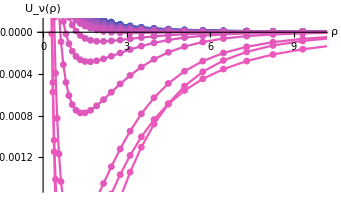

```mathematica
UChannelData[νi_]:=Table[{Exp[gridFun[r00]+ni*(gridFun[rr]-gridFun[r00])/nMax],Sort[UνEigenList[LengthOfBasisSet][[ni,1]],Greater][[νi]]},{ni,1,nMax}];
U[νi_,r_]:=Interpolation[UChannelData[νi]][r];
UChannelData[15]

For[iCh=1,iCh≤LengthOfBasisSet,iCh++,
	fileU=OpenWrite[prefixDirectory<>"\\outputs\\U_adiabats\\UchannelData_"<>ToString[offset]<>"_D_"<>ToString[De]<>"_r0_"<>ToString[ρ0]<>"_"<>ToString[iCh]<>".dat"];
	Export[fileU,UChannelData[iCh]];
	Close[fileU];
];
Show[Table[ListLinePlot[UChannelData[νi],PlotStyle->RGBColor[.234+νi/50,.34,.735],PlotMarkers->{Automatic,Small}],{νi,1,LengthOfBasisSet}],PlotRange->{{.0,10},{-.0015,.0001}},LabelStyle->{Large,Black},AxesLabel->{"ρ","U_ν(ρ)"}]
```

{{0.169367,0.0148157},{0.191234,0.0116212},{0.215924,0.00911542},{0.243802,0.00714996},{0.275279,0.00560829},{0.310821,0.00439904},{0.350951,0.00345052},{0.396262,0.00270653},{0.447424,0.00212295},{0.505191,0.0016652},{0.570417,0.00130615},{0.644063,0.00102452},{0.727219,0.000803614},{0.82111,0.00063034},{0.927124,0.000494427},{1.04683,0.000387819},{1.18198,0.000304198},{1.33459,0.000238607},{1.5069,0.000187159},{1.70145,0.000146804},{1.92113,0.00011515},{2.16917,0.0000903216},{2.44923,0.0000708466},{2.76545,0.0000555707},{3.1225,0.0000435886},{3.52565,0.0000341901},{3.98084,0.0000268181},{4.49481,0.0000210356},{5.07514,0.0000164999},{5.73039,0.0000129422},{6.47025,0.0000101516},{7.30563,7.96275×10^-6},{8.24886,6.24583×10^-6},{9.31387,4.89911×10^-6},{10.5164,3.84277×10^-6},{11.8742,3.01419×10^-6},{13.4072,2.36428×10^-6},{15.1383,1.85449×10^-6},{17.0928,1.45463×10^-6},{19.2996,1.14098×10^-6},{21.7914,8.94967×10^-7},{24.6049,7.01995×10^-7},{27.7817,5.50632×10^-7},{31.3686,4.31905×10^-7},{35.4186,3.38778×10^-7},{39.9915,2.65731×10^-7},{45.1548,2.08434×10^-7},{50.9848,1.63492×10^-7},{57.5674,1.2824×10^-7},{65.,1.00589×10^-7}}

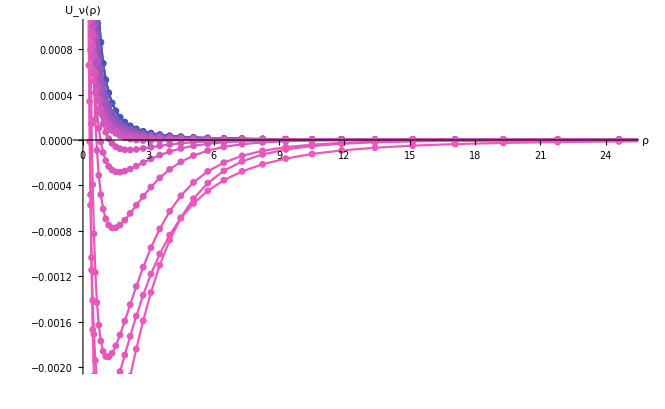

```mathematica
UChannelData[νi_]:=Table[{Exp[gridFun[r00]+ni*(gridFun[rr]-gridFun[r00])/nMax],Sort[UνEigenList[LengthOfBasisSet][[ni,1]],Greater][[νi]]},{ni,1,nMax}];
U[νi_,r_]:=Interpolation[UChannelData[νi]][r];
UChannelData[14]
Show[Table[ListLinePlot[UChannelData[νi],PlotStyle->RGBColor[.234+νi/50,.34,.735],PlotMarkers->{Automatic,Small}],{νi,1,LengthOfBasisSet}],PlotRange->{{.05,25},{-.002,.001}},LabelStyle->{Large,Black},AxesLabel->{"ρ","U_ν(ρ)"}]
```

```mathematica
(*Test algorithm efficiency:*)
ν1=14;ν2=14;
Flist=  FListMap[   Table[  QuantumList⟦ν1,modelSet⟦k⟧ ⟧,{k,1,Length[modelSet]}]  ];
FlistPrim= FListMap[   Table[  QuantumList⟦ν2,modelSet⟦k⟧ ⟧,{k,1,Length[modelSet]}]];
If[Length[Flist]≠ Length[FlistPrim],Print["Length[Flist]≠ Length[FlistPrim]"]; ];(*Tu się może zepsuć ^*)
								
sumFun=vU*Sum[ Flist⟦i⟧*FlistPrim⟦i⟧ ,{i,1,Length[Flist]}];
NIntegrate[Exp[I*(QuantumList⟦ν1,2⟧-QuantumList⟦ν2,2⟧)*ϕ/2]*sumFun * Vtot[.1,vU,ϕ],{vU,0,1},{ϕ,0,4*π},AccuracyGoal->8,Method->{"Trapezoidal"}]//AbsoluteTiming
```

### 3. Perform DVR

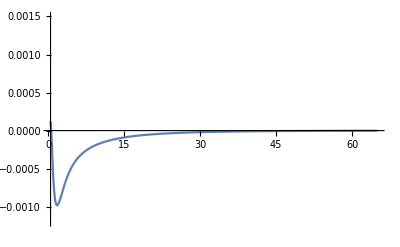

```mathematica
iChnl = 35;offs = 210*0;
Uchannel=Import[prefixDirectory<>"\\outputs\\U_adiabats\\UchannelData_"<>ToString[offs]<>"_D_0.03_r0_2_"<>ToString[iChnl]<>".dat"];
Unu=Interpolation[Uchannel];
Uch[x_]:=Unu[x];Plot[Uch[x],{x,0.5,65},PlotRange->{{0.5,65},{-0.0012,0.0015}}]
```

```mathematica
fileName="DVR_energies_3bodyAdiabat_"<>ToString[offs]<>"_Ch_"<>ToString[iChnl]<>"_D_"<>ToString[De]<>"_r0_"<>ToString[ρ0]<>".dat"
(*fileName="DVR_energies_VTB_D_"<>ToString[De]<>"_r0_"<>ToString[ρ0]<>".dat"*)
Print["mred -> mred3"];mred=mred3;			 				 			 				 				 		 				 				 

  r00=0.18; rr= (*10000 R4*)65;   nn=2000; 
printLine="-";Do[printLine=StringJoin[printLine,"-"],{i,1,50}];

																(* construct Matrix T  *)
gridFun[r_]:=Log[r];
matrixT=IdentityMatrix[(nn-1)];

	ii=Range[nn-1];
		mii=Table[Range[nn-1],{i,1,nn-1}];
		mjj=Transpose[mii];
		
		mid=IdentityMatrix[IntegerPart[(nn-1)]];
		ipj=mii+mjj+mid;
		imj=mii-mjj+mid;
		
		matrixT=(-1)^(imj)/4.*Pi^2/mred/(gridFun[rr]-gridFun[r00])^2*(1./Sin[(imj)*Pi/nn/2.]^2-1./Sin[(ipj)*Pi/nn/2.]^2)*1/Exp[2*gridFun[r00]+ipj*(gridFun[rr]-gridFun[r00])/nn];
		matrixT=matrixT-DiagonalMatrix[Diagonal[matrixT]];
		newdiag=DiagonalMatrix[1./4./mred*Pi^2/(gridFun[rr]-gridFun[r00])^2*((2.*nn^2+1.)/3.-1./Sin[Pi*ii/nn]^2)*1./(Exp[gridFun[r00]+ii*(gridFun[rr]-gridFun[r00])/nn])^2-1./4./mred/Exp[2.*(gridFun[r00]+ii*(gridFun[rr]-gridFun[r00])/nn)]+3./8./mred/Exp[2.*(gridFun[r00]+ii*(gridFun[rr]-gridFun[r00])/nn)]];
matrixT=matrixT+newdiag;



fileEnRoVibToLatex=OpenWrite[prefixDirectory<>"\\outputs\\"<>fileName];



		tableJVofEn={};tableofJVEn ={};tablevPsi={};
		l=0;Eigen={0};
		While[l≠1(*Length[Eigen]≠0*),

			Print["J = ",l];
			
																(* construct Matrix T + V and find eigenvalues *)
			(*VplusBarrier[r_]:=VXK2Tiemann[r]+l(l+1)/(2 mred r^2);*)
			(*VplusBarrier[r_]:=VTB[r,De,ρ0]+l(l+1)/(2 mred r^2);*)
			VplusBarrier[r_]:=Uch[r];
		
			matrixV=IdentityMatrix[(nn-1)];
			Do[matrixV⟦i,i⟧=VplusBarrier[Exp[gridFun[r00]+i*(gridFun[rr]-gridFun[r00])/nn]]
									,{i,1,nn-1}];
									
			Eigen=Select[Sort[N[Eigenvalues[matrixT+matrixV]] (*/cmtoEh*)],Negative];
			AppendTo[tableJVofEn,Eigen];
			Print["Eigenvalues for all v: ",Eigen];Print[printLine,printLine];
			
			(*
																	(* vibrational states, construct ψ *)
		    (* exportIntTable={};	*)
		    If[l==0,
				For[v=1,v≤Length[Eigen],v++,
					
					If[Abs[Eigen⟦v⟧]<0.00001,Continue[]]; (*Threshold for eigen selection here!!!!!*)
					(*fileWvFs=OpenWrite[prefixDirectory<>"\\outputs\\Psis\\DVR_Wvfs_VTB_D_"<>ToString[De]<>"_r0_"<>ToString[ρ0]<>"_J_0_v_"<>ToString[v]<>".dat"];
					fileEigens=OpenWrite[prefixDirectory<>"\\outputs\\Eigens\\DVR_Eigens_VTB_D_"<>ToString[De]<>"_r0_"<>ToString[ρ0]<>"_J_0_v_"<>ToString[v]<>".dat"];*)
					file3Body=OpenWrite[prefixDirectory<>"\\outputs\\Psis\\DVR_Psis_3bodyAdiabat_Ch_"<>ToString[iChnl]<>"_D_"<>ToString[De]<>"_r0_"<>ToString[ρ0]<>"_v_"<>ToString[v]<>".dat"];
					
					(*root1=FindRoot[VplusBarrier[x]==Eigen[[v]],{x,0.05}];
					root2=FindRoot[VplusBarrier[x]==Eigen[[v]],{x,5.0}];*)
					
					System=Eigensystem[matrixT+matrixV];
					EnSystem=Select[Sort[(System⟦1⟧)],Negative];
					VecSystem=System⟦  2, Position[System⟦1⟧,EnSystem⟦v⟧]⟦1,1⟧ ⟧;
					Psiv={};
					
					For[i=1,i<nn,i++,
						xi=(Exp[gridFun[r00]+i*(gridFun[rr]-gridFun[r00])/nn]);
						AppendTo[Psiv,{xi,VecSystem⟦i⟧}]
						];
					
					Export[file3Body,Psiv];
					Close[file3Body];
					
					Export[fileWvFs,Psiv];
					Export[fileEigens,{{root1[[1,2]]*0,Eigen⟦v⟧},{Abs[root2[[1,2]]],Eigen⟦v⟧}}];
					Close[fileWvFs];Close[fileEigens];
				
				(*inPsiv=Interpolation[Psiv⟦All,{1,2}⟧]; (*Psiv⟦All,{1,2}⟧==Psiv -- LOL*)
	
																	(* Plot and calculate <ψ | r | ψ >*)
	
				(*Print[Show[Plot[inPsiv[r],{r,2,20}],ListPlot[Psiv]]];*)
				r0=NIntegrate[r inPsiv[r]^2,{r,r00,rr}]/NIntegrate[inPsiv[r]^2,{r,r00,rr}];
				AppendTo[exportIntTable,{"J =",l,"v =",v,"∫rψ(r)^2 dr =",r0,If[v==Length[Eigen]-1,"\n",""]}];
				(*Print["v = ",v, "/∫r ψ(r)^2dr = ", r0,"/"];If[v≠Length[Eigen]-1,Print["-------------------------------"]]*)
			 *)	];
				];*)
			l++;			
			];
	
	tableofJVEn = Flatten[Table[ {aJ-1,aV-1,tableJVofEn⟦aJ,aV⟧} ,{ aJ,1,Length[tableJVofEn] },{ aV,1,Length[tableJVofEn⟦aJ⟧] }],1];



tableToExport =  tableofJVEn; 
Export[fileEnRoVibToLatex,tableToExport];

Close[fileEnRoVibToLatex];
```

DVR_energies_3bodyAdiabat_1160_Ch_35_D_0.03_r0_2.dat

mred -> mred3

J = 0

Eigenvalues for all v: {-0.00277079,-0.00251275,-0.00227025,-0.00204292,-0.00183038,-0.00163231,-0.00144831,-0.00127797,-0.00112086,-0.000976522,-0.000844575,-0.000725147,-0.000619896,-0.00053142,-0.000455485,-0.000388603,-0.000330604,-0.000280032,-0.000236096,-0.000198132,-0.000165379,-0.000137177,-0.000112987,-0.0000923831,-0.0000749219,-0.0000602221,-0.0000479309,-0.0000377102,-0.0000292829,-0.0000224145,-0.0000168792,-0.0000124842,-9.0494×10^-6,-6.40609×10^-6,-4.39625×10^-6,-2.84337×10^-6,-1.65918×10^-6,-9.19279×10^-7,-4.14759×10^-7}

------------------------------------------------------------------------------------------------------

```mathematica
Needs["NumericalCalculus`"];
FM=FindMinimum[Uch[r],{r,6.5}];		
R0=FM[[2,1,2]]
D0=-FM[[1]]/cmtoEh
B0=1/(2*mred3*R0^2)/cmtoEh;
der=ND[Uch[x],{x,2},R0];
w0=Sqrt[der/mred3]/cmtoEh
```

InterpolatingFunction::dmval: Input value {-68.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.79632

215.208

28.6089

```mathematica
Streams[] (*all streams*)
ostr=Select[Streams[],SameQ[Head[#],OutputStream]&] (*select inputStreamsonly*);
Close[#]&/@ostr (*now close all the input streams...*);
Streams[] (*only output streams remain*)
```

{OutputStream[…],OutputStream[…],OutputStream[…],OutputStream[…],OutputStream[…],OutputStream[…]}

Close::spfile: Cannot close special file ….

{OutputStream[…],OutputStream[…]}

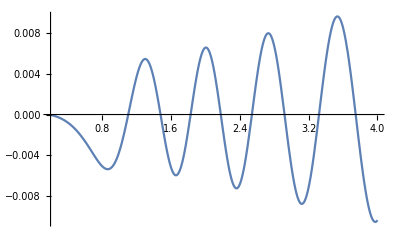

```mathematica
inPsiv=Interpolation[Psiv⟦All,{1,2}⟧];
Plot[inPsiv[x],{x,.2,4}]
```

### 4. Plot the positions of atoms in hyperspherical coords

```mathematica
(*Animation*)
Manipulate[
Rcm = 0;xmax=ymax=zmax=20;

a = {Rcm,Rcm,Rcm};
b={0,0};
at1 = (invJacr[1]/.HypSpherMap)/.{ρ->rho,α->alph,θξ->thxi,ϕξ->phixi,θη->thet,ϕη->phiet};
at2 = (invJacr[2]/.HypSpherMap)/.{ρ->rho,α->alph,θξ->thxi,ϕξ->phixi,θη->thet,ϕη->phiet};
at3 = (invJacr[3]/.HypSpherMap)/.{ρ->rho,α->alph,θξ->thxi,ϕξ->phixi,θη->thet,ϕη->phiet};

jacξ=(vec[ξ]/.HypSpherMap)/.{ρ->rho,α->alph,θξ->thxi,ϕξ->phixi,θη->thet,ϕη->phiet};
jacη=(vec[η]/.HypSpherMap)/.{ρ->rho,α->alph,θξ->thxi,ϕξ->phixi,θη->thet,ϕη->phiet};

perpξη = (Cross[vec[ξ],vec[η]]/.HypSpherMap)/.{ρ->rho,α->alph,θξ->thxi,ϕξ->phixi,θη->thet,ϕη->phiet};
planeVers1 = {perpξη⟦2⟧,-perpξη⟦1⟧,0};
planeVers2 = {perpξη⟦1⟧ perpξη⟦3⟧,perpξη⟦2⟧ perpξη⟦3⟧,-perpξη⟦2⟧^2-perpξη⟦1⟧^2};


prlξ= -mred3^(1/2) (vec2d[ξ]/.HypPlanePrlMap)/.{ρ->rho,θ->th,ϕ->phi};
prlη= -mred3^(1/2) (vec2d[η]/.HypPlanePrlMap)/.{ρ->rho,θ->th,ϕ->phi};

planeat1= Delete[-mred3^(1/2)invJacr[1]/.HypPlanePrlMap,{3}] /.{ρ->rho,θ->th,ϕ->phi}; (* our jacobi = -mred3^(1/2) prl jacobi *)
planeat2= Delete[-mred3^(1/2)invJacr[2]/.HypPlanePrlMap,{3}] /.{ρ->rho,θ->th,ϕ->phi};
planeat3= Delete[-mred3^(1/2)invJacr[3]/.HypPlanePrlMap,{3}] /.{ρ->rho,θ->th,ϕ->phi};

Graphics3D[{{PointSize[.01],Point[a]},
{Red, Arrow[{a, at1}]},{Green, Arrow[{a, at2}]},{Blue, Arrow[{a, at3}]},
{Gray, Arrow[{a, 10 planeVers2/Norm[planeVers2]}]},{GrayLevel[0.4], Arrow[{a, 10 planeVers1/Norm[planeVers1]}]},
(*{Opacity[0.3,Yellow],InfinitePlane[a,{at2,at3}]},*)
{Orange, Arrow[{a, jacξ/5}]},{Brown, Arrow[{a, jacη/5}]}}, 
Axes -> True, Boxed -> True, 
AxesLabel -> {x, y, z},
PlotLabel->"r[2,3] = "<>ToString[r[2,3]/.{ρ->rho,α->alph,θξ->thxi,ϕξ->phixi,θη->thet,ϕη->phiet}]<>" r[1,2] = "<>ToString[r[1,2]/.{ρ->rho,α->alph,θξ->thxi,ϕξ->phixi,θη->thet,ϕη->phiet}]<>" r[3,1] = "<>ToString[r[3,1]/.{ρ->rho,α->alph,θξ->thxi,ϕξ->phixi,θη->thet,ϕη->phiet}],
PlotRange->{{-xmax,xmax},{-ymax,ymax},{-zmax,zmax}}
]

Graphics[{
{Brown, Arrow[{b, {((planeVers1/Norm[planeVers1]).jacη),((planeVers2/Norm[planeVers2]).jacη)}}/5]},
{Orange, Arrow[{b, {((planeVers1/Norm[planeVers1]).jacξ),((planeVers2/Norm[planeVers2]).jacξ)}}/5]},
{Magenta, Arrow[{b, prlξ/5}]},
{Purple, Arrow[{b, prlη/5}]},
{Red, Arrow[{b, {((planeVers1/Norm[planeVers1]).at1),((planeVers2/Norm[planeVers2]).at1)}}]},
{Green, Arrow[{b, {((planeVers1/Norm[planeVers1]).at2),((planeVers2/Norm[planeVers2]).at2)}}]},
{Blue, Arrow[{b, {((planeVers1/Norm[planeVers1]).at3),((planeVers2/Norm[planeVers2]).at3)}}]},
{LightRed, Arrow[{b, planeat1}]},
{LightGreen, Arrow[{b, planeat2}]},
{LightBlue, Arrow[{b, planeat3}]}
}


,Frame->True,Axes->True,PlotRange->{{-xmax,xmax},{-ymax,ymax}},
PlotLabel->"r23 = "<>ToString[3^(-1/4) rho/mred3^(1/2) (1+Sin[th]Sin[phi-5π/6])^(1/2)]<>" r12 = "<>ToString[3^(-1/4) rho/mred3^(1/2) (1+Sin[th]Sin[phi-π/6])^(1/2)]<>" r31 = "<>ToString[3^(-1/4) rho/mred3^(1/2) (1+Sin[th]Sin[phi+π/2])^(1/2)]

]

,{rho,1 ,150 },{alph,0.01,π/2},{thxi,0.01,π},{phixi,0.01,2π},{thet,0.01,π},{phiet,0.01,2π},{th,0,π/2},{phi,0,2 π/3}]
```

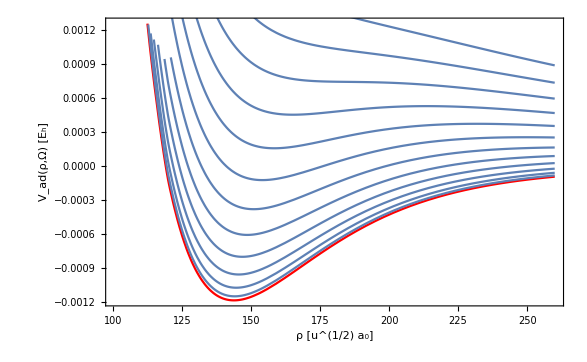

```mathematica
(*Print the hyperpotentials for different K at given Ω*)
ρmin = 100.5;
ρmax = 260;
kmin=50;kmax=520;kIncr=40;
Show[
		Join[{Plot[ℏ^2(1(1+4) + 15/4)/(Eh 2 (x u^.5 a0)^2)+(VaK2Tiemann[(r[2,3])/.{α->π/6}/.{θξ->π/12}/.{ϕξ->π/3}/.{θη->π/3}/.{ϕη->π/3}]+ VaK2Tiemann[(r[3,1])/.{α->π/6}/.{θξ->π/12}/.{ϕξ->π/3}/.{θη->π/3}/.{ϕη->π/3}] + VaK2Tiemann[(r[1,2])/.{α->π/6}/.{θξ->π/12}/.{ϕξ->π/3}/.{θη->π/3}/.{ϕη->π/3}])/.{ρ->x},{x,ρmin     ,ρmax    },PlotStyle->Red]},
		Table[Print[ki];Plot[ℏ^2(ki(ki+4) + 15/4)/(Eh 2 (x u^.5 a0)^2)+(VaK2Tiemann[(r[2,3])/.{α->π/6}/.{θξ->π/12}/.{ϕξ->π/3}/.{θη->π/3}/.{ϕη->π/3}]+ VaK2Tiemann[(r[3,1])/.{α->π/6}/.{θξ->π/12}/.{ϕξ->π/3}/.{θη->π/3}/.{ϕη->π/3}] + VaK2Tiemann[(r[1,2])/.{α->π/6}/.{θξ->π/12}/.{ϕξ->π/3}/.{θη->π/3}/.{ϕη->π/3}])/.{ρ->x},{x,ρmin     ,ρmax    }],{ki,kmin,kmax,kIncr}]],
			Frame->True,FrameLabel->{"ρ [u^(1/2) a_0]","V_ad(ρ,Ω) [E_h]"},LabelStyle-> {FontSize->40,Black}]
```

### 5. Check that -1/2(Δ_ξ + Δ_η) = -1/(2 ρ^2) ((∂_ρ)^2 + 5ρ ∂_ρ + K^2)

```mathematica
TestFun[name_,Coord_]:=name[Sequence@@Coord]; (* <- one can define any function name[Coord] and check that the code works *)
Coord = {ρ,α,θξ,ϕξ,θη,ϕη};
CoordMap={ρ Cos[α] Sin[θξ] Cos[ϕξ],
		  ρ Cos[α] Sin[θξ] Sin[ϕξ],
		  ρ Cos[α] Cos[θξ] ,
		  ρ Sin[α] Sin[θη] Cos[ϕη],
		  ρ Sin[α] Sin[θη] Sin[ϕη],
		  ρ Sin[α] Cos[θη]};
CoordJac=Table[ D[CoordMap⟦j⟧,Coord⟦i⟧]  ,{i,Length[CoordMap]},{j,Length[CoordMap]}];
ivJac = Simplify[Inverse[CoordJac]];
Det[CoordJac];
OpDi[fun_,ithCoord_]:=  (ivJac.Table[D[fun,Coord⟦i⟧],{i,Length[Coord]}])⟦ithCoord⟧;
DelSq[coord_,fun_] := FullSimplify[Sum[Nest[OpDi[#,i]&,fun,2],{i,Length[Coord]}]];

l=1;m=0;μ=0;λ=2;k=3;
κ = (k - l - λ)/2;

FullSimplify[-(1/2) DelSq[Coord,Subscript[F, ν][ρ] Φ[α,θξ,ϕξ,θη,ϕη]]/Φ[α,θξ,ϕξ,θη,ϕη] ]
FullSimplify[-(1/2) DelSq[Coord, Φ[α,θξ,ϕξ,θη,ϕη]]/Φ[α,θξ,ϕξ,θη,ϕη] + (15/4)/(2ρ^2)]
(*Check*)
Solve[x^2+4x-21==0,{x}]
Clear@l;Clear@λ;Clear@μ;Clear@m;Clear@k;Clear@κ;
```

(21 F_ν[ρ]-ρ (5 F_ν'[ρ]+ρ F_ν''[ρ]))/(2 ρ^2)

99/(8 ρ^2)

{{x→-7},{x→3}}

### 6. Check that -1/2(Δ_(r_1 r_2 r_3)) = -1/2(Δ_ξ + Δ_η)

```mathematica
(* Write the kinetic energy operator in transformed coordinates: x->f1(coords), y->f2(coords), z->f3(coords)   *)
Clear@m1;Clear@m2;Clear@m3;
Coord = {R,θ,ϕ};
CoordMap={x = R Sin[θ]Cos[ϕ],
		  y = R Sin[θ]Sin[ϕ],
		  z = R Cos[θ]};
CoordJac=Table[ D[CoordMap⟦j⟧,Coord⟦i⟧]  ,{i,Length[CoordMap]},{j,Length[CoordMap]}];
ivJac = Simplify[Inverse[CoordJac]];
OpDi[fun_,ithCoord_]:=  (ivJac.Table[D[fun,Coord⟦i⟧],{i,Length[Coord]}])⟦ithCoord⟧;
DelSq[coord_,fun_] := FullSimplify[
						Sum[Nest[OpDi[#,i]&,fun,2],{i,Length[Coord]}]
						];
(*-DelSq[Coord,TestFun[Coord]]*)


(* Write the kinetic energy operator in transformed coordinates, but now we already know: coord1 -> f(x,y,z), coord2 -> f(x,y,z) ...   *)
Clear[x];Clear[y];Clear[z];
CoordMap = Flatten[FullSimplify[{(m1 m2 / (m1 + m2))^0.5 (r[1]-r[2]),
								(m3(m1 + m2)/(m1 + m2 + m3))^0.5 (  (m1 r[1] + m2 r[2])/(m1+m2) - r[3] ),
								(m1 r[1] + m2 r[2] + m3 r[3] )/(m1+m2+m3)
					}]];
CartCoord = Flatten[{r[1],r[2],r[3]}];
Coord = Flatten[{vec[ξ],vec[η],vec[Rcm]}];


invCoordJac = Simplify[Table[ D[CoordMap⟦j⟧,CartCoord⟦i⟧]  ,{i,Length[CoordMap]},{j,Length[CoordMap]}]] ;

OpDi[fun_,ithCoord_]:=  (invCoordJac.Table[D[fun,Coord⟦i⟧],{i,Length[Coord]}])⟦ithCoord⟧;
OpT[fun_] := -FullSimplify[Sum[ Nest[OpDi[#,i]&,fun,2] ,{i,1,3}]/(2 m1) + 
						   Sum[ Nest[OpDi[#,i]&,fun,2],{i,4,6}]/(2 m2) + 
						   Sum[ Nest[OpDi[#,i]&,fun,2],{i,7,9}]/(2 m3) ];


OpTonψ = OpT[TestFun[ψ,Coord]];
FullSimplify[Collect[OpTonψ,Derivative[___][ψ][Sequence@@Coord]]]
```

1/((m1+m2)^2 (m1+m2+m3)^2)(-0.5 (1. m1+1. m2)^2 (m1+m2+m3) ψ^(0,0,0,0,0,0,0,0,2)[ξ[1],ξ[2],ξ[3],η[1],η[2],η[3],0[1],0[2],0[3]]-0.5 (1. m1+1. m2)^2 (m1+m2+m3) ψ^(0,0,0,0,0,0,0,2,0)[ξ[1],ξ[2],ξ[3],η[1],η[2],η[3],0[1],0[2],0[3]]-0.5 (1. m1+1. m2)^2 (m1+m2+m3) ψ^(0,0,0,0,0,0,2,0,0)[ξ[1],ξ[2],ξ[3],η[1],η[2],η[3],0[1],0[2],0[3]]-0.5 (m1+m2)^2 (1. m1^2+2. m1 m2+1. m2^2+2. m1 m3+2. m2 m3+1. m3^2) ψ^(0,0,0,0,0,2,0,0,0)[ξ[1],ξ[2],ξ[3],η[1],η[2],η[3],0[1],0[2],0[3]]-0.5 (m1+m2)^2 (1. m1^2+2. m1 m2+1. m2^2+2. m1 m3+2. m2 m3+1. m3^2) ψ^(0,0,0,0,2,0,0,0,0)[ξ[1],ξ[2],ξ[3],η[1],η[2],η[3],0[1],0[2],0[3]]-0.5 (m1+m2)^2 (1. m1^2+2. m1 m2+1. m2^2+2. m1 m3+2. m2 m3+1. m3^2) ψ^(0,0,0,2,0,0,0,0,0)[ξ[1],ξ[2],ξ[3],η[1],η[2],η[3],0[1],0[2],0[3]]-0.5 (m1+m2+m3) (1. m1^3+m2^2 (1. m2+1. m3)+m1^2 (3. m2+1. m3)+m1 m2 (3. m2+2. m3)) ψ^(0,0,2,0,0,0,0,0,0)[ξ[1],ξ[2],ξ[3],η[1],η[2],η[3],0[1],0[2],0[3]]-0.5 (m1+m2+m3) (1. m1^3+m2^2 (1. m2+1. m3)+m1^2 (3. m2+1. m3)+m1 m2 (3. m2+2. m3)) ψ^(0,2,0,0,0,0,0,0,0)[ξ[1],ξ[2],ξ[3],η[1],η[2],η[3],0[1],0[2],0[3]]-0.5 (m1+m2+m3) (1. m1^3+m2^2 (1. m2+1. m3)+m1^2 (3. m2+1. m3)+m1 m2 (3. m2+2. m3)) ψ^(2,0,0,0,0,0,0,0,0)[ξ[1],ξ[2],ξ[3],η[1],η[2],η[3],0[1],0[2],0[3]])

```mathematica
(*Proof of concept: ψ(ρ) = Ψ(ρ)/ρ^(5/2) *)
F[r] = G[r]/(r^(5/2));
FullSimplify[  -1/2 (D[F[r],{r,2}] + 5/ r D[F[r],{r,1}]) ]
```

(15 G[r]-4 r^2 G''[r])/(8 r^(9/2))

```mathematica
(*Example of the plots of Vtot and hypercentrifugal barrier*)
k=301;
ρmin = 45.5;
ρmax = 80;
Show[Table[Plot[ℏ^2(j(j+4) + 15/4)/(Eh 2 (x u^.5 a0)^2),{x,ρmin     ,ρmax  },PlotStyle->{Red,Thin}],{j,350,450,15}]]
Plot[(VXK2Tiemann[(r[2,3]u^.5)/.{α->0}]+ VXK2Tiemann[(r[3,1]u^.5)/.{α->0}] + VXK2Tiemann[(r[1,2]u^.5)/.{α->0}])/.{ρ->x},{x,ρmin     ,ρmax    }]
```

### 7. Check recurrence pattern in hyperangular

```mathematica
f[u] = (1+u)^((ν+n)/4) (1-u)^((ν-n)/4) w[u];
FullSimplify[(-4/u) FullSimplify[D[FullSimplify[u*(1-u^2)D[f[u],{u,1}]],{u,1}]]]
```

-(√(1-u) (3 (-2+u+7 u^2) w[u]+4 (-1+u) ((-1+3 u+6 u^2) w'[u]+u (-1+u^2) w''[u])))/u

```mathematica
FullSimplify[% +(f[u]/(1-u^2))*(ν^2+n^2-2ν n u) +(4f[u]/u^2)(1/2)(j(j+1)-n^2)-f[u]*k(k+4)]
```

((1-u)^(3/2) ((-18+2 j (1+j)+u (6-(-3+k) (7+k) u)) w[u]+4 u ((-1+3 u+6 u^2) w'[u]+u (-1+u^2) w''[u])))/u^2

```mathematica
FullSimplify[% +  (4/u^2) (1-u^2)^(1/2) (1/4)((j-n+2)(j-n+1)(j+n-1)(j+n))^(1/2)( (1+u)^((ν+n-2)/4) (1-u)^((ν-n+2)/4) wnm2[u])  +  (4/u^2) (1-u^2)^(1/2)  (1/4)((j-n)(j-n-1)(j+n+1)(j+n+2))^(1/2)( (1+u)^((ν+n+2)/4) (1-u)^((ν-n-2)/4) wnp2[u])]
```

1/u^2(1-u)^(3/2) ((-18+2 j (1+j)+u (6-(-3+k) (7+k) u)) w[u]-√((-4+j) (-3+j) (4+j) (5+j)) (-1+u) wnm2[u]+√((-2+j) (-1+j) (2+j) (3+j)) wnp2[u]+√((-2+j) (-1+j) (2+j) (3+j)) u wnp2[u]+4 u ((-1+3 u+6 u^2) w'[u]+u (-1+u^2) w''[u]))

```mathematica
res = %
```

1/u^2(1-u)^(3/2) ((-18+2 j (1+j)+u (6-(-3+k) (7+k) u)) w[u]-√((-4+j) (-3+j) (4+j) (5+j)) (-1+u) wnm2[u]+√((-2+j) (-1+j) (2+j) (3+j)) wnp2[u]+√((-2+j) (-1+j) (2+j) (3+j)) u wnp2[u]+4 u ((-1+3 u+6 u^2) w'[u]+u (-1+u^2) w''[u]))

```mathematica
FullSimplify[res/.{w[u]-> Sum[b[n,k]u^k,{k,0,kmax}],w'[u]-> Sum[k b[n,k]u^(k-1),{k,1,kmax}],
w''[u]-> Sum[k (k-1) b[n,k]u^(k-2),{k,2,kmax}],
wnm2[u]->  Sum[b[n-2,k]u^k,{k,0,kmax}],wnp2[u]->  Sum[b[n+2,k]u^k,{k,0,kmax}]}]
```

1/u^2(1-u)^(1/4 (-n+ν)) (1+u)^((n+ν)/4) (-√((1+j-n) (2+j-n) (-1+j+n) (j+n)) (-1+u) ∑_(k=0)^kmax u^k b[-2+n,k]+4 u (u (-1+u^2) ∑_(k=2)^kmax (-1+k) k u^(-2+k) b[n,k]+(-1-n u+u^2 (3+ν)) ∑_(k=1)^kmax k u^(-1+k) b[n,k])+(2 j (1+j)-2 n^2-2 n u-u^2 (k-ν) (4+k+ν)) ∑_(k=0)^kmax u^k b[n,k]+√((-1+j-n) (j-n) (1+j+n) (2+j+n)) (1+u) ∑_(k=0)^kmax u^k b[2+n,k])

```mathematica
FullSimplify[% / (4/u^2(1-u)^(1/4 (-n+ν)) (1+u)^((n+ν)/4))]
```

1/4 (-√((1+j-n) (2+j-n) (-1+j+n) (j+n)) (-1+u) ∑_(k=0)^kmax u^k b[-2+n,k]+4 u (u (-1+u^2) ∑_(k=2)^kmax (-1+k) k u^(-2+k) b[n,k]+(-1-n u+u^2 (3+ν)) ∑_(k=1)^kmax k u^(-1+k) b[n,k])+(2 j (1+j)-2 n^2-2 n u-u^2 (k-ν) (4+k+ν)) ∑_(k=0)^kmax u^k b[n,k]+√((-1+j-n) (j-n) (1+j+n) (2+j+n)) (1+u) ∑_(k=0)^kmax u^k b[2+n,k])

```mathematica
res2=%
```

1/4 (-√((1+j-n) (2+j-n) (-1+j+n) (j+n)) (-1+u) ∑_(k=0)^kmax u^k b[-2+n,k]+4 u (u (-1+u^2) ∑_(k=2)^kmax (-1+k) k u^(-2+k) b[n,k]+(-1-n u+u^2 (3+ν)) ∑_(k=1)^kmax k u^(-1+k) b[n,k])+(2 j (1+j)-2 n^2-2 n u-u^2 (k-ν) (4+k+ν)) ∑_(k=0)^kmax u^k b[n,k]+√((-1+j-n) (j-n) (1+j+n) (2+j+n)) (1+u) ∑_(k=0)^kmax u^k b[2+n,k])

```mathematica
Expand[FullSimplify[(-1/4)(k-ν)(4+k+ν)  + (k-2)(3+ν) + (k-3)(k-2)]]
Expand[FullSimplify[((k+ν)/2+2+k-2)((k-ν)/2-k+2)]]
```

-3 k+(3 k^2)/4-ν+k ν+ν^2/4

3 k-(3 k^2)/4+ν-k ν-ν^2/4

```mathematica
FullSimplify[-n (k-1) -n/2]
```

1/2 (n-2 k n)

```mathematica
FullSimplify[  -k(k-1)-k+(1/4)(2j(j+1)-2n^2)]
```

1/2 (j+j^2-2 k^2-n^2)